```mathematica
fileX="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\The Malcolm Project\\B_Three Sections\\Profiles_2_21_2020\\Bx_Average_11Mags_smooth.txt";
fileY="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\The Malcolm Project\\B_Three Sections\\Profiles_2_21_2020\\By_Average_11Mags_smooth.txt";
```

```mathematica
fileX="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\The Malcolm Project\\B_Three Sections\\Profiles_2_21_2020\\Bx_Average_11Mags_step.txt";
fileY="C:\\Users\\jsten\\Documents\\Reaserch\\Majorana spin\\The Malcolm Project\\B_Three Sections\\Profiles_2_21_2020\\By_Average_11Mags_step.txt";
```

```mathematica
MagX={};
For[l=1,l≤151,l++,
out=Import[fileX,{"Lines",l}];
mtp=ToExpression[out];
MagX=Join[MagX,{mtp}];
];
```

```mathematica
MagY={};
For[l=1,l≤151,l++,
out=Import[fileY,{"Lines",l}];
mtp=ToExpression[out];
MagY=Join[MagY,{mtp}];
];
```

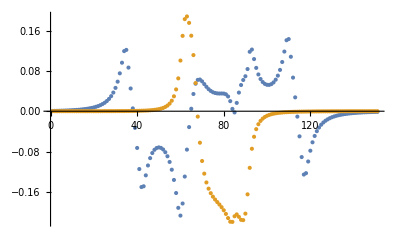

```mathematica
ListPlot[{MagX,MagY},PlotRange->All]
```

```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250-25;
NxM=50;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw*0;
tsw=4.0;
μ=0.0;
gx=30;
gy=30;
B=2Δ;

(*tϕ=ts/200;*)
tϕ1=0.4*ts;
tϕ2=ts;
αϕ=0.0;
```

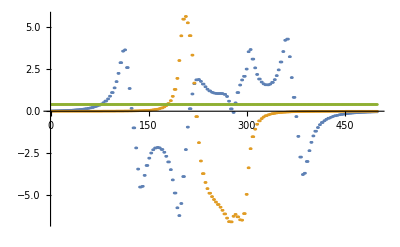

```mathematica
(*Currently MagΔ is being used*)
MagΔX=Table[gx*MagX[[Ceiling[ii*Length[MagX]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
MagΔY=Table[gy*MagY[[Ceiling[ii*Length[MagY]/(2Nx+NxM)]]],{ii,1,2Nx+NxM}];
Δprofile=Table[Δ,{i,1,2Nx+NxM}];

ListPlot[{MagΔX,MagΔY,Δprofile},PlotRange->All]
```

```mathematica
H[ϕ_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(2Nx+NxM+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[i]],{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[i]],{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[Nx+i]],{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[Nx+i]] ,{i,1,NxM}],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+i]],{i,1,NxM}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+i]] ,{i,1,NxM}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0+MagΔY[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->Table[-μ+ϵ0-MagΔY[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->Table[MagΔX[[Nx+NxM+i]] ,{i,1,Nx}],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0},{HM1,HMM,HM2},{0,H2M,H22}}]];

Hsp
];
```

```mathematica
H0=H[0.];
{e0,ψ0}=Transpose[Sort[Transpose[Eigensystem[H0,-10]]]];
```

```mathematica
e0
```

{-0.215442,-0.0774183,-0.0104601,-0.00588332,-0.00414507,0.00414507,0.00588332,0.0104601,0.0774183,0.215442}

```mathematica
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,


Hsp=H[ϕ];


etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];


Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];
```

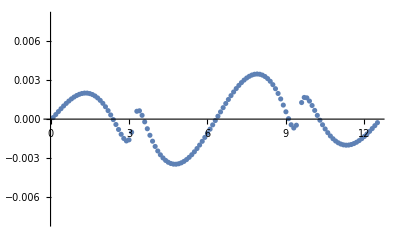

```mathematica
ListPlot[Re[Iϕ]]
```

```mathematica
a=SessionTime[];
Iθ={};
Imax={};
For[θM=0.0,θM≤2π,θM+=0.01 π,
eϕ={};
elϕ=Table[{},{n,1,10}];
For[ϕ=0,ϕ≤4π,ϕ+=0.1,


(*Full Wire*)
Hsp=H[ϕ,θM];



etp=Sort[Eigenvalues[Hsp,-10]];
For[n=1,n≤Length[etp],n++,
elϕ[[n]]=Join[elϕ[[n]],{{ϕ,etp[[n]]}}]
];
If[π<ϕ<3π,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2+1]]+etp[[Length[etp]/2+2]]}}];
,
eϕ=Join[eϕ,{{ϕ,Sum[etp[[i]],{i,1,Length[etp]/2-2}]+etp[[Length[etp]/2-1]]+etp[[Length[etp]/2]]}}];
];


];

Iϕ={};
IϕM={};
For[ϕi=2,ϕi≤Length[eϕ],ϕi++,
Iϕ=Join[Iϕ,{{eϕ[[ϕi,1]],(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])}}];
IϕM=Join[IϕM,{Re[(eϕ[[ϕi,2]]-eϕ[[ϕi-1,2]])/(eϕ[[ϕi,1]]-eϕ[[ϕi-1,1]])]}];
];

Iθ=Join[Iθ,{Iϕ}];
Imax=Join[Imax,{{θM,Max[IϕM]}}];
Print[{θM,Max[IϕM]}];
];
```

{0.,0.00218023}

{0.0314159,0.00215367}

{0.0628319,0.00212663}

{0.0942478,0.00209912}

{0.125664,0.00207116}

{0.15708,0.00204274}

{0.188496,0.00201389}

{0.219911,0.00198461}

{0.251327,0.00195492}

{0.282743,0.00192483}

{0.314159,0.00189434}

{0.345575,0.00186347}

{0.376991,0.00183223}

{0.408407,0.00180064}

{0.439823,0.00176872}

{0.471239,0.00173646}

{0.502655,0.0017039}

{0.534071,0.00167104}

{0.565487,0.0016379}

{0.596903,0.0016045}

{0.628319,0.00157086}

{0.659734,0.001537}

{0.69115,0.00150293}

{0.722566,0.00146868}

{0.753982,0.00143426}

{0.785398,0.00139972}

{0.816814,0.00136506}

{0.84823,0.00133032}

{0.879646,0.00129552}

{0.911062,0.00126071}

{0.942478,0.00122591}

{0.973894,0.00119115}

{1.00531,0.00115649}

{1.03673,0.00112197}

{1.06814,0.00108762}

{1.09956,0.00105352}

{1.13097,0.00101971}

{1.16239,0.000986256}

{1.19381,0.000953236}

{1.22522,0.000920726}

{1.25664,0.000888813}

{1.28805,0.000857595}

{1.31947,0.000827178}

{1.35088,0.000797681}

{1.3823,0.000769235}

{1.41372,0.000741985}

{1.44513,0.000716086}

{1.47655,0.000691707}

{1.50796,0.000669028}

{1.53938,0.000648236}

{1.5708,0.000629523}

{1.60221,0.000613076}

{1.63363,0.00059907}

{1.66504,0.000587659}

{1.69646,0.000578964}

{1.72788,0.000573064}

{1.75929,0.000569976}

{1.79071,0.000569617}

{1.82212,0.000571801}

{1.85354,0.000576299}

{1.88496,0.000582869}

{1.91637,0.000591223}

{1.94779,0.000601023}

{1.9792,0.000611893}

{2.01062,0.000623845}

{2.04204,0.000641084}

{2.07345,0.000658012}

{2.10487,0.000674156}

{2.13628,0.000689019}

{2.1677,0.000702084}

{2.19911,0.000712817}

{2.23053,0.000720672}

{2.26195,0.000725114}

{2.29336,0.000725654}

{2.32478,0.0007219}

{2.35619,0.000713641}

{2.38761,0.000700956}

{2.41903,0.000684349}

{2.45044,0.000664906}

{2.48186,0.000644433}

{2.51327,0.000625522}

{2.54469,0.000611425}

{2.57611,0.000605621}

{2.60752,0.000611059}

{2.63894,0.000629334}

{2.67035,0.000660282}

{2.70177,0.000702266}

{2.73319,0.000752858}

{2.7646,0.000809511}

{2.79602,0.000869957}

{2.82743,0.000932374}

{2.85885,0.000995397}

{2.89027,0.00105805}

{2.92168,0.00111969}

{2.9531,0.00117989}

{2.98451,0.00123841}

{3.01593,0.00129512}

{3.04734,0.00134999}

{3.07876,0.00140304}

{3.11018,0.0014543}

{3.14159,0.00150384}

{3.17301,0.00155175}

{3.20442,0.0015981}

{3.23584,0.00164298}

{3.26726,0.00168645}

{3.29867,0.0017286}

{3.33009,0.00176949}

{3.3615,0.00180918}

{3.39292,0.00184779}

{3.42434,0.00188663}

{3.45575,0.00192435}

{3.48717,0.00196099}

{3.51858,0.00199659}

{3.55,0.0020312}

{3.58142,0.00206484}

{3.61283,0.00209756}

{3.64425,0.00212937}

{3.67566,0.00216031}

{3.70708,0.0021904}

{3.7385,0.00221966}

{3.76991,0.00224811}

{3.80133,0.00227575}

{3.83274,0.00230258}

{3.86416,0.0023286}

{3.89557,0.00235382}

{3.92699,0.00237824}

{3.95841,0.00240189}

{3.98982,0.00242476}

{4.02124,0.00244687}

{4.05265,0.00246821}

{4.08407,0.00248881}

{4.11549,0.00250865}

{4.1469,0.00252775}

{4.17832,0.0025461}

{4.20973,0.00256372}

{4.24115,0.00258059}

{4.27257,0.00259673}

{4.30398,0.00261214}

{4.3354,0.00262681}

{4.36681,0.00264075}

{4.39823,0.00265396}

{4.42965,0.00266644}

{4.46106,0.00267819}

{4.49248,0.00268921}

{4.52389,0.00269951}

{4.55531,0.00270908}

{4.58673,0.00271793}

{4.61814,0.00272605}

{4.64956,0.00273345}

{4.68097,0.00274012}

{4.71239,0.00274607}

{4.7438,0.00275131}

{4.77522,0.00275582}

{4.80664,0.00275962}

{4.83805,0.00276269}

{4.86947,0.00276506}

{4.90088,0.0027667}

{4.9323,0.00276764}

{4.96372,0.00276786}

{4.99513,0.00276738}

{5.02655,0.00276619}

{5.05796,0.00276429}

{5.08938,0.0027617}

{5.1208,0.0027584}

{5.15221,0.0027544}

{5.18363,0.00274971}

{5.21504,0.00274433}

{5.24646,0.00273825}

{5.27788,0.00273149}

{5.30929,0.00272405}

{5.34071,0.00271593}

{5.37212,0.00270714}

{5.40354,0.00269767}

{5.43496,0.00268753}

{5.46637,0.00267673}

{5.49779,0.00266527}

{5.5292,0.00265315}

{5.56062,0.00264039}

{5.59203,0.00262697}

{5.62345,0.00261292}

{5.65487,0.00259823}

{5.68628,0.00258291}

{5.7177,0.00256696}

{5.74911,0.0025504}

{5.78053,0.00253322}

{5.81195,0.00251543}

{5.84336,0.00249704}

{5.87478,0.00247806}

{5.90619,0.00245848}

{5.93761,0.00243832}

{5.96903,0.00241759}

{6.00044,0.00239629}

{6.03186,0.00237442}

{6.06327,0.002352}

{6.09469,0.00232904}

{6.12611,0.00230554}

{6.15752,0.0022815}

{6.18894,0.00225695}

{6.22035,0.00223187}

{6.25177,0.0022063}

{6.28319,0.00218023}

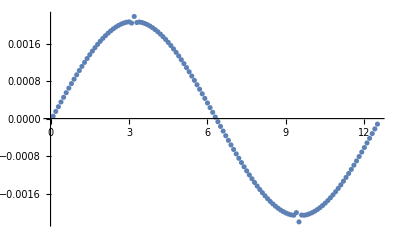

```mathematica
ListPlot[Re[Iθ[[1]]],PlotRange->All]
```

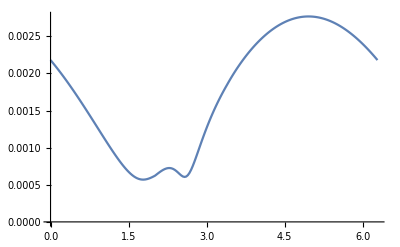

```mathematica
ListPlot[Imax,Joined->True]
```